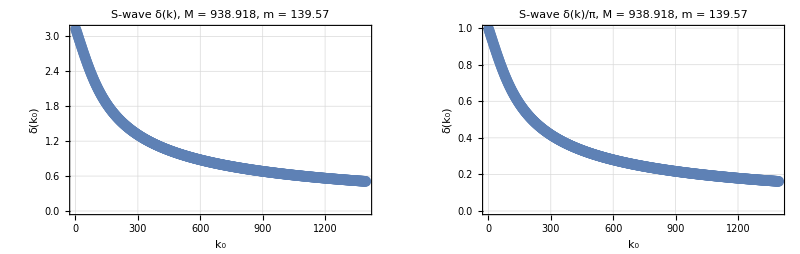

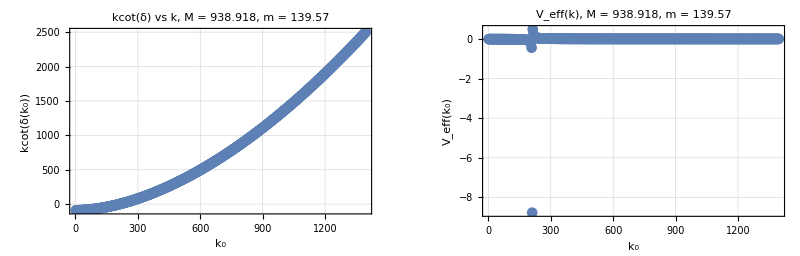

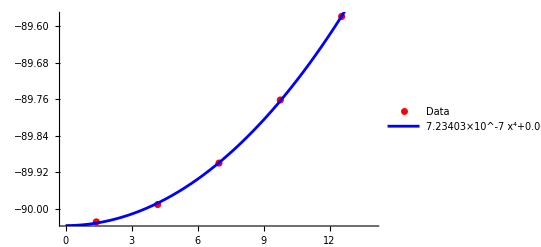

```mathematica
(*---PARAMETERS---*)
M=938.918;                (* Mass of Nucleon M=938.918*)
m=139.570;               (*Pion mass m=139.570*)
α=0.5;              (*Depth of Yukawa potential, 0.128351*)
r0=10^-6;          (*Small value near r=0 for boundary condition*)
l=0;

kMin = m/100;
kMax = 10*m; 
kSpacing = (kMax-kMin)/500(*0.01*m^2*);
λ = 2*Pi/Abs[m]; (* De Broglie Wavelength*)
rMax=10*λ;           (*Max radius for numerical integration, ensures asymptotic behavior by being much larger than λ*)
fitStart=0.8*rMax;       (*Start of asymptotic region*)
fitEnd=rMax;         (*End of asymptotic region*)
fitSpacing = rMax/100;    (* Interval spacing in asymptotic region*)

(*---Yukawa Potential---*)
V[r_]:=-α*Exp[-m*r]/r+l(l+1)/(M*r^2);

(*---Phase Shift Extractor---*)
ClearAll[extractPhaseShift]

extractPhaseShift[k0_?Positive,rm_?Positive,M_?Positive]:=Module[{k,sol,uFunc,data,fit,δ},k=k0;
(*Numerical solution to Schrödinger equation*)sol=NDSolve[{u''[r]==(M*V[r]-k0^2) u[r],u[r0]==r0^(l+1),u'[r0]==1},u,{r,r0,rm},MaxSteps->Infinity];
(*Wavefunction interpolator*)uFunc=Function[r,Evaluate[u[r]/. sol[[1]]]];
(*Sample numerical wavefunction in asymptotic region*)data=Table[{r,uFunc[r]},{r,0.8*rm,rm,rm/100}];
(*Fit to A*Sin[k*r+δ] to extract phase shift*)fit=NonlinearModelFit[data,A*Sin[k*r-l*Pi/2+δ],{{A,1},{δ,0}},r,MaxIterations->∞]; (*MaxIterations->∞*)
(*Return δ modulo π (optional,depending on context)*)Mod[δ/. fit["BestFitParameters"],Pi](*δ/.fit["BestFitParameters"]*)]

(*---Phase Shift Curve Generator---*)
kRange=Range[kMin,kMax,kSpacing];  (*k's to test*)
rMaxList =(10*(2 Pi/#))&/@kRange;
pairs = Transpose[{kRange,rMaxList}];

(*phaseShiftData=Table[{k0,extractPhaseShift[k0,M]},{k0,kRange}];*)

(* ---Loop through the values of k_n and rmax_n to construct the data--- *)
phaseShiftData=ParallelTable[{kRange[[i]],extractPhaseShift[kRange[[i]],rMaxList[[i]],M]},{i,Length[kRange]}]; 

(* ---Make the phases continuous by gluing together the pieces--- *)
unwrapPhaseReverse[data_]:=Module[{ks,deltas,unwrapped,shifts,jumpIndices},{ks,deltas}=Transpose[data];
unwrapped=deltas;
Do[If[unwrapped[[i]]-unwrapped[[i-1]]>Pi/2,(*Apply+π to all previous values*)unwrapped[[1;;i-1]]+=Pi;],{i,2,Length[unwrapped]}];
Transpose[{ks,unwrapped}]];

phaseShiftDataUnwrapped=unwrapPhaseReverse[phaseShiftData];

(*---Plot the phase shift vs k---*)
dplot = ListPlot[phaseShiftData,PlotMarkers->Automatic,AxesLabel->{"k₀","δ(k₀)"},PlotLabel->Row[{"S-wave δ(k), M = ",M,", m = ",m}],Frame->True,GridLines->Automatic,PlotRange->{Automatic,All},PerformanceGoal->"Speed",PlotMarkers->None];
dplotstitched = ListPlot[{#[[1]],#[[2]]/Pi}&/@phaseShiftDataUnwrapped,PlotMarkers->Automatic,AxesLabel->{"k₀","δ(k₀)"},PlotLabel->Row[{"S-wave δ(k)/π, M = ",M,", m = ",m}],Frame->True,GridLines->Automatic,PlotRange->{Automatic,All},PerformanceGoal->"Speed",PlotMarkers->None];

GraphicsGrid[{{dplot,dplotstitched}},ImageSize->800]

kmax=m/10;
kcotd = {#[[1]],#[[1]]*Cot[#[[2]]]}&/@phaseShiftDataUnwrapped;
veff = {#[[1]],1/(#[[1]]*Cot[#[[2]]])}&/@phaseShiftDataUnwrapped;
kcotdlowk=Select[kcotd,#[[1]]<=kmax&];
vefflowk = Select[veff,#[[1]]<=kmax&];
cotdrootIm= {#[[1]],Cot[#[[2]]]}&/@phaseShiftDataUnwrapped;
(*scatlen= {#[[1]],-#[[2]]}&/@phaseShiftData1Unwrapped;-del[0,V0,0.001]/0.001*)

kcotdfit = Fit[kcotd,{1,x^2,x^4},x];
kcotdfitlowk4= Fit[kcotdlowk,{1,x^2,x^4},x];
kcotdfitlowk2=Normal[Series[kcotdfitlowk4,{x,0,2}]];


kcotdplot = ListPlot[kcotd,PlotMarkers->Automatic,AxesLabel->{"k₀","kcot(δ(k₀))"},PlotLabel->Row[{"kcot(δ) vs k, M = ",M,", m = ",m}],Frame->True,GridLines->Automatic,PlotRange->{Automatic,All},PerformanceGoal->"Speed",PlotMarkers->None];
veffplot = ListPlot[veff,PlotMarkers->Automatic,AxesLabel->{"k₀","V_eff(k₀)"},PlotLabel->Row[{"V_eff(k), M = ",M,", m = ",m}],Frame->True,GridLines->Automatic,PlotRange->{Automatic,All},PerformanceGoal->"Speed",PlotMarkers->None];

GraphicsGrid[{{kcotdplot,veffplot}},ImageSize->800]

kcotdlowkplot = Show[ListPlot[kcotdlowk,PlotStyle->Red,PlotLegends->{"Data"}, PlotRange->{{0,kmax},Automatic},PerformanceGoal->"Speed",PlotMarkers->None],Plot[kcotdfitlowk4,{x,0,kmax},PlotStyle->Blue,PlotLegends->{ToString[TraditionalForm[kcotdfitlowk4]]}]]
```

```mathematica
(*kcotdzeroes=Select[Partition[kcotd,2,1],Sign[#[[1,2]]]!=Sign[#[[2,2]]]&]
kp=4.570525;
residuedelta=0.1; (*adjust based on data resolution*)
nearPolePoints=Select[veff,0<Abs[#[[1]]-kp]<residuedelta&];
residueEstimates=(#1[[1]]-kp)*#1[[2]]&/@nearPolePoints;
kr=Mean[residueEstimates];
y=Sqrt[2*kr*kp/M];
Δ=kp^2/M;*)
```

{{x→0.-48.2288 ⅈ},{x→0.+109.166 ⅈ}}

1

2

3

InterpolatingFunction::dmval: Input value {-63.4966} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-12.0925} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-3.07422} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

4

InterpolatingFunction::dmval: Input value {-63.4966349432341142921584759973} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-12.0925035536469385605867613915} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-3.07421650219935181961790980703} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

0.0567171333629444587064231745532

5

InterpolatingFunction::dmval: Input value {0.0567171333629444587064231745532} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0285122} lies outside the range of data in the interpolating function. Extrapolation will be used.

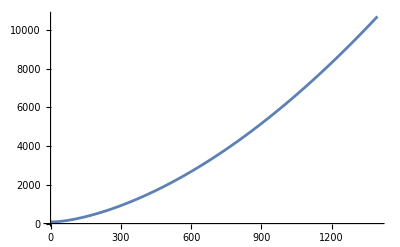

InterpolatingFunction::dmval: Input value {0.0285122} lies outside the range of data in the interpolating function. Extrapolation will be used.

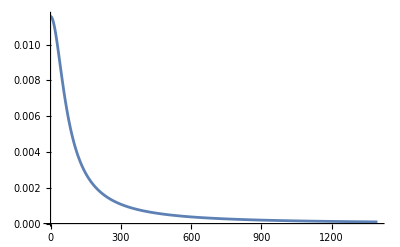

```mathematica
Solve[kcotdfitlowk2-I*x==0]
1
kcotdInterp = Interpolation[kcotd];
2
(* Define function an left and right of the pole so that it doesnt smooth over pole structure*)
veffInterp[k_]=1/kcotdInterp[k];
3
kp1= x/.FindRoot[kcotdInterp[x]==0,{x,100}];
4
kp=x/. FindRoot[kcotdInterp[x]==0,{x,100},WorkingPrecision->30,AccuracyGoal->20]
5

kcotdInterpprime=kcotdInterp';
residue=1/kcotdInterpprime[kp];

(*Double checking residue makes sense*)(* IT DOESNT RIGHT NOW, USE FIRST DEF*)
(* Define function an left and right of the pole so that it doesnt smooth over pole structure*)
(*kcotdInterpleft1=Interpolation[Select[kcotd,First[#]<=kp+0.05&]];
kcotdInterpright1=Interpolation[Select[kcotd,First[#]>=kp-0.05&]];
veffInterpleft1[x_]:=1/kcotdInterpleft1[x];
veffInterpright1[x_]:=1/kcotdInterpright1[x];
resLeft=(kp-10^(-11)-kp)*veffInterpleft1[kp-10^(-11)];
resRight=(kp+10^(-11)-kp)*veffInterpright1[kp+10^(-11)];
residue1=N[(resLeft+resRight)/2];
kcotdInterpleft1["Domain"];
kcotdInterpright1["Domain"];*)
(*---*)

kr=residue;

y=Sqrt[2*kr*kp/M];
Δ=kp^2/M;
Plot[kcotdInterp[x],{x,0,kMax},PlotRange->All]
Plot[veffInterp[x],{x,0,kMax},PlotRange->All]
(*Res[zr_]:=2*zr*(z-zr)*V[z]/.{z->zr+10^(-11)};*)
```

InterpolatingFunction::dmval: Input value {0.0285122} lies outside the range of data in the interpolating function. Extrapolation will be used.

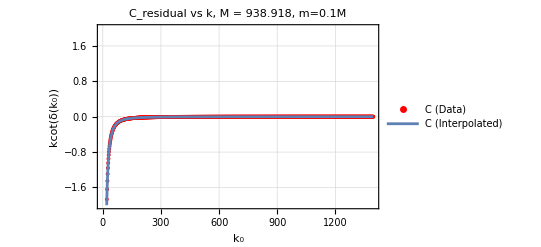

-105.473

-105.473+108.219 (-2.7914+k1)-66.3827 (-2.7914+k1)^2

-105.473+108.219 (-2.7914+k1)-66.3827 (-2.7914+k1)^2+13.5384 (-2.7914+k1)^3

-105.473+108.219 (-2.7914+k1)-66.3827 (-2.7914+k1)^2+13.5384 (-2.7914+k1)^3

InterpolatingFunction::dmval: Input value {0.0285122} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

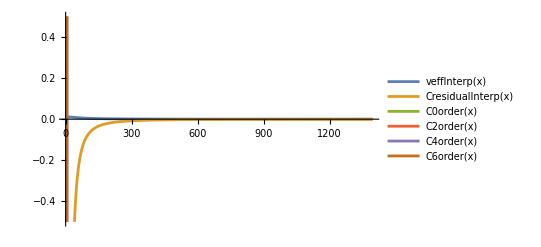

InterpolatingFunction::dmval: Input value {1.27452×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

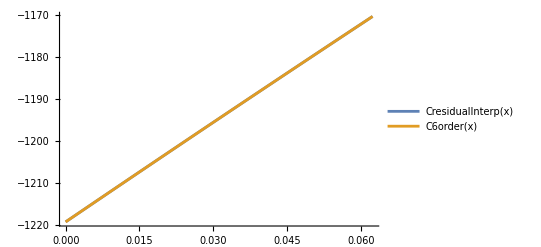

InterpolatingFunction::dmval: Input value {0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

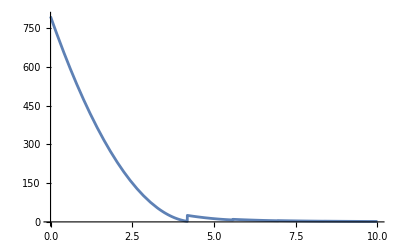

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

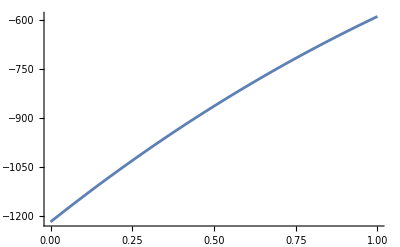

```mathematica
Cresidual = {#[[1]],#[[2]]-y^2/(#[[1]]^2/M-Δ)}&/@veff;
CresidualInterp = Interpolation[Cresidual];
Show[ListPlot[Cresidual,PlotStyle->{Red,PointSize[0.007]},AxesLabel->{"k₀","kcot(δ(k₀))"},PlotLabel->Row[{"C_residual vs k, M = ",M,", m=0.1M"}],Frame->True,GridLines->Automatic,PlotTheme->"Detailed",PlotRange->{Automatic,{-2,2}},PlotLegends->{"C (Data)"}],
Plot[CresidualInterp[x],{x,0,kMax},PlotStyle->{PointSize[0.007]},AxesLabel->{"k₀","kcot(δ(k₀))"},PlotLabel->Row[{"C_residual (interpolated) vs k, M = ",M,", m=0.1M"}],Frame->True,GridLines->Automatic,PlotTheme->"Detailed",PlotRange->{Automatic,{-2,2}},PlotLegends->{"C (Interpolated)"}]]

(*Cresidualtaylor1[k0_,n_]:=Module[{taylorTerms,k},taylorTerms=Table[Derivative[m][CresidualInterp][k0]/m!*(k-k0)^m,{m,0,n}];
Total[taylorTerms]];
CresidualTaylor[k0_?NumericQ,n_Integer?NonNegative]:=Function[k,Sum[Derivative[m][CresidualInterp][k0]/Factorial[m]*(k-k0)^m,{m,0,n}]];
C0=CresidualTaylor[1,0];
C2=CresidualTaylor[1,2];
C4=CresidualTaylor[1,4];
C6=CresidualTaylor[1,6];*)

k0=2*kMin;

f0=CresidualInterp[k0];
f1=Derivative[1][CresidualInterp][k0];
f2=Derivative[2][CresidualInterp][k0];
f3=Derivative[3][CresidualInterp][k0];
f4=Derivative[4][CresidualInterp][k0];
f5=Derivative[5][CresidualInterp][k0];
f6=Derivative[6][CresidualInterp][k0];

C0order[k1_]=f0
C2order[k1_]=f0+f1*(k1-k0)+f2/2*(k1-k0)^2
C4order[k1_]=f0+f1*(k1-k0)+f2/2*(k1-k0)^2+f3/6*(k1-k0)^3+f4/24*(k1-k0)^4
C6order[k1_]=f0+f1*(k1-k0)+f2/2*(k1-k0)^2+f3/6*(k1-k0)^3+f4/24*(k1-k0)^4+f5/120*(k1-k0)^5+f6/720*(k1-k0)^6


Plot[{veffInterp[x],CresidualInterp[x],C0order[x],C2order[x],C4order[x],C6order[x]},{x,0,kMax},PlotRange->{Automatic,{-0.5,0.5}},PlotLegends->"Expressions"]
Plot[{CresidualInterp[x],C6order[x]},{x,0,1.1*kp},PlotLegends->"Expressions"]
Plot[D[CresidualInterp[s],{s,1}]/.{s->x},{x,0,10}]
Plot[CresidualInterp[x],{x,0,1},PlotLegends->"Expressions"]
```

-0.150241

-6.65598

InterpolatingFunction::dmval: Input value {0.0285122} lies outside the range of data in the interpolating function. Extrapolation will be used.

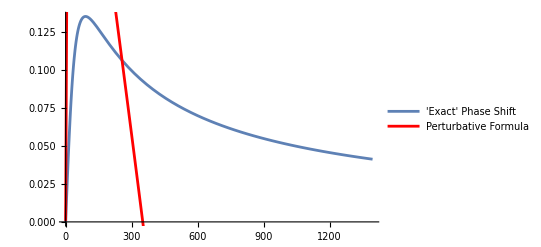

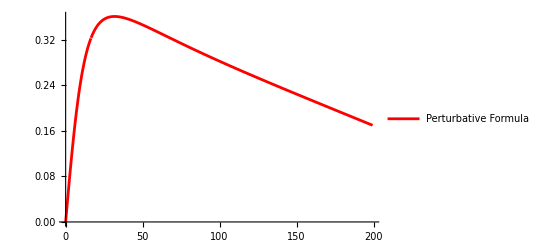

```mathematica
C01S0 = -3.34*(2.568×10^−5); (*fm^2 = 2.568×10^−5 MeV^-2,  -3.63 fm^2, −3.34 fm^2*)
C21S0 = 3.24*(2.568×10^−5)^2; (*2.92 fm^4, 3.24 fm^4 *)
D21S0 = -0.42*(2.568×10^−5)^2; (*0, -0.42*)
μ=m;
gA=Sqrt[4*Pi*α]; (*1.27 experimentally, α=gA^2/4π -> α=0.128351*)
fπ=132;

Am1[k_] = -C01S0/(1+C01S0*M/(4Pi)(μ+I*k));
A01[k_]=-C21S0*k^2*(Am1[k]/C01S0)^2;
A02[k_]=gA^2/(2fπ^2)(-1+m^2/(4k^2)Log[1+4k^2/m^2]);
A03[k_]=gA^2/fπ^2(m*M*Am1[k]/(4Pi))(-(μ+I*k)/m+m/(2k)(ArcTan[2k/m]+I/2Log[1+4k^2/m^2]));
A04[k_]=gA^2/(2fπ^2)(m*M*Am1[k]/(4Pi))^2(-((μ+I*k)/m)^2+(I*ArcTan[2k/m]-1/2Log[(m^2+4k^2)/μ^2]+1));
A05[k_]=-D21S0*m^2(Am1[k]/C01S0)^2;
A0[k_]=A01[k]+A02[k]+A03[k]+A04[k]+A05[k];

delta0[k_]=1/(2I)Log[1+I*M*k/(2Pi)Am1[k]];
delta1[k_]=M*k/(4Pi)(A0[k]/(1+I*M*k/(2Pi)Am1[k]));
deltatot[k_]=delta0[k]+delta1[k];

deltajustpion[k_]=M*k*A02[k]/(4Pi);

a1 = 1/(m+4Pi/(M*C01S0)-4Pi*D21S0*m^2/(M*C01S0^2))
1/a1

dplotstitchedinterp = Interpolation[{#[[1]],#[[2]]/Pi}&/@phaseShiftData1Unwrapped];
Show[Plot[dplotstitchedinterp[x],{x,0,kMax},PlotLegends->{"'Exact' Phase Shift"}],Plot[1/Pi(deltatot[x]),{x,0,kMax},PlotStyle->Red,PlotLegends->{"Perturbative Formula"},PlotRange->All]]
Plot[1/Pi(deltatot[x]),{x,0,kMax/7},PlotStyle->Red,PlotLegends->{"Perturbative Formula"},PlotRange->All]
```